```mathematica
SetOptions[Plot,AspectRatio->Automatic];
tf:=TableForm;tx:=TeXForm;hh:=Hold;
ss:=Simplify;
tt[x_]:=TraditionalForm[x];
mf:=MatrixForm;


split[x_]:=2 x/;x<.5;split[x_]:=3(x-1)^2/;x>.5
```

```mathematica
Split
```

Split

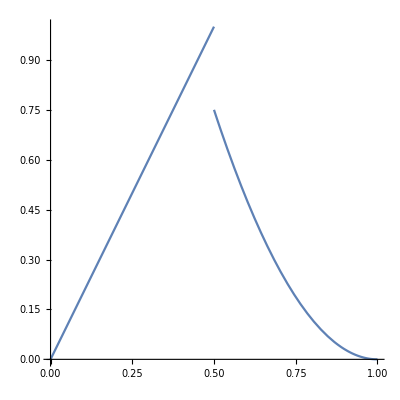

```mathematica
Plot[split[x],{x,0,1},AspectRatio->1,Exclusions->{.5}]
```

```mathematica
Finite
```

Finite

```mathematica
finite[1]=3;finite[2]=3;finite[3]=2;finite[6]=1
```

1

```mathematica
nodel[ch_,p_]:=Text[Style[ch,14,Bold],p]
```

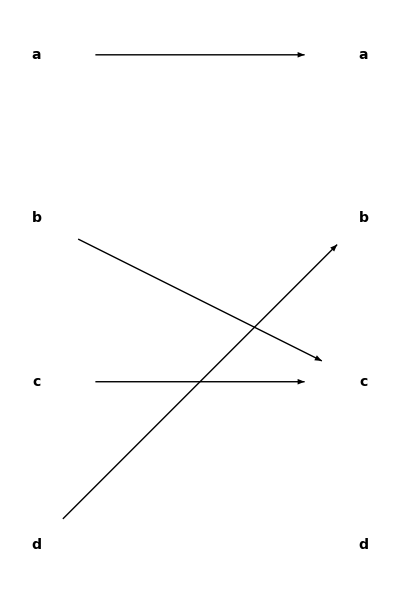

```mathematica
Module[{s=.18,a=.15},Show[
Graphics[{Arrowheads[a],
nodel["a",{1,4}],nodel["b",{1,3}],nodel["c",{1,2}],nodel["d",{1,1}],nodel["a",{0,4}],nodel["b",{0,3}],nodel["c",{0,2}],nodel["d",{0,1}],Arrow[{{0,4},{1,4}},s],Arrow[{{0,3},{1,2}},s],Arrow[{{0,2},{1,2}},s],Arrow[{{0,1},{1,3}},s]
}
],
ImageSize->Tiny,AspectRatio->1.5]
]
```

```mathematica
Fresnel
```

Fresnel

```mathematica
fs[x_]:=Integrate[Sin[t^2],{t,0,x}]
```

```mathematica
fs[2]
```

√(π/2) FresnelS[2 √(2/π)]

```mathematica
fs[2]//N
```

0.804776

```mathematica
units[xmin_,xmax_]:=Range[Floor[xmin],Floor[xmax],1]
```

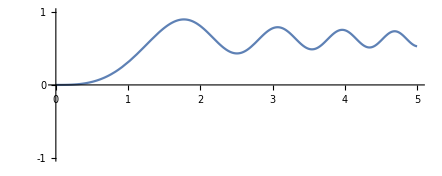

```mathematica
fsplot=Plot[fs[x],{x,0,5},PlotRange->{{0,5},{-1,1}},AspectRatio->.4,Ticks->units]
```

```mathematica
Sine Blur
```

Blur Sine

```mathematica
sb[x_]:=Sin[10/x]
```

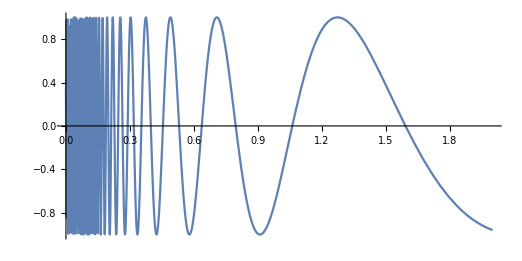

```mathematica
Plot[sb[x],{x,0,2},AspectRatio->.5]
```

```mathematica
Derivative
```

Derivative

```mathematica
st2[x_]:=Sin[x^2]
```

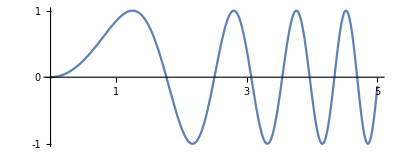

```mathematica
st2plot=Plot[st2[x],{x,0,5},AspectRatio->.4, Ticks->units]
```

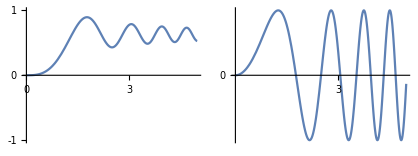

```mathematica
Show[
Graphics[
{
Inset[fsplot,{0,0}],
Inset[Style[" ⟹ ",16],{1.6,0}],
Inset[st2plot,{3,0}]
},AspectRatio->.3
]
]
```